# Classification workflows monad

## Introduction

In this document we describe the design and implementation of a (software programming) monad for classification workflows specification and execution. The design and implementation are done with Mathematica / Wolfram Language (WL).

The goal of the monad design is to make the specification of classification workflows (relatively) easy, straightforward, by following a certain main scenario and specifying variations over that scenario.

The monad is named ClCon and it is based on the State monad package “StateMonadCodeGenerator.m”, [AAp1, AA1], the classifier ensembles package “ClassifierEnsembles.m”, [AAp4, AA2], and the package for Receiver Operating Characteristic (ROC) functions calculation and plotting “ROCFunctions.m”, [AAp5, AA2, Wk2].

The data for this document is read from WL’s repository using the package “GetMachineLearningDataset.m”, [AAp10].

The monadic programming design is used as a Software Design Pattern. The ClCon monad can be also seen as a Domain Specific Language (DSL) for the specification and programming of machine learning classification workflows.

Here is an example of using the ClCon monad over the Titanic data:

ClConUnit[dsTitanic] ⟹ | (* lift the data to the monad *)
  ClConSplitData[0.75] ⟹ | (* split the data *)
  ClConMakeClassifier["LogisticRegression"] ⟹ | (* create a classifier *)
  ClConClassifierMeasurements[{"Accuracy","Precision","Recall"}] ⟹ | (* compute classifier measurements *)
  ClConEchoValue | (* display the current pipeline value *)

value: <|Accuracy→0.75841,Precision→<|died→0.818653,survived→0.671642|>,Recall→<|died→0.782178,survived→0.72|>|>

Remark: The table above is produced with the TraceMonad of the paclet "MonadMakers" and some of the explanations below also utilize that package.

As it was mentioned above the monad ClCon can be seen as a DSL. Because of this the monad pipelines made with ClCon are sometimes called “specifications”.

## Paclet load

The following commands load the packages [AAp1--AAp10, AAp12]:

Load the paclet

```mathematica
Needs["AntonAntonov`MonadicContextualClassification`"]
```

## Data load

In this section we load data that is used in the rest of the document. The “quick” data is created in order to specify quick, illustrative computations.

Remark: In all datasets the classification labels are in the last column.

The summarization of the data is done through ClCon, which in turn uses the function RecordsSummary from the paclet "DataReshapers".

### WL resources data

The following commands produce datasets using the package [AAp10] (that utilizes ExampleData):

```mathematica
dsTitanic=ResourceFunction["ExampleDataset"][{"MachineLearning","Titanic"}];
dsMushroom=ResourceFunction["ExampleDataset"][{"MachineLearning","Mushroom"}];
dsWineQuality=ResourceFunction["ExampleDataset"][{"MachineLearning","WineQuality"}];
dsWineQuality=(Join[KeyDrop[#1,{"wine quality (score between 1-10)"}],Association["wineQuality"->#1["wine quality (score between 1-10)"]]]&)/@dsWineQuality;
```

Here is are the dimensions of the datasets:

```mathematica
Dataset[Dataset[Map[Prepend[Dimensions[ToExpression[#]],#]&,{"dsTitanic","dsMushroom","dsWineQuality"}]][All,AssociationThread[{"name","rows","columns"},#]&]]
```

Here is the summary of dsTitanic:

```mathematica
ClConUnit[dsTitanic]⟹ClConSummarizeData["MaxTallies"->12];
```

summaries:  {Anonymous→{1 passenger class
3rd | 709
1st | 323
2nd | 277,2 passenger age
Min | 0.1667
1st Qu | 21.
Median | 28.
Mean | 29.8811
3rd Qu | 39.
Max | 80.
Missing[___] | 263,3 passenger sex
male | 843
female | 466,4 passenger survival
died | 809
survived | 500}}

Here is the summary of dsMushroom in long form:

```mathematica
ClConUnit[dsMushroom]⟹ClConSummarizeDataLongForm["MaxTallies"->12];
```

summaries:  {Anonymous→{1 RowID
1 | 23
10 | 23
100 | 23
1000 | 23
1001 | 23
1002 | 23
1003 | 23
1004 | 23
1005 | 23
1006 | 23
1007 | 23
(Other) | 129559,2 Variable
bruises? | 5644
cap-color | 5644
cap-shape | 5644
cap-surface | 5644
edibility of mushroom (either edible or poisonous) | 5644
gill-attachment | 5644
gill-color | 5644
gill-size | 5644
gill-spacing | 5644
habitat | 5644
odor | 5644
(Other) | 67728,3 Value
white | 13854
smooth | 8540
partial | 5644
free | 5626
one | 5488
brown | 5012
broad | 4940
close | 4620
bulbous | 3776
gray | 3504
pink | 3496
(Other) | 65312}}

Here is the summary of dsWineQuality in long form:

```mathematica
ClConUnit[dsWineQuality]⟹ClConSummarizeDataLongForm["MaxTallies"->12];
```

summaries:  {Anonymous→{1 RowID
1 | 12
10 | 12
100 | 12
1000 | 12
1001 | 12
1002 | 12
1003 | 12
1004 | 12
1005 | 12
1006 | 12
1007 | 12
(Other) | 58625,2 Variable
alcohol | 4898
chlorides | 4898
density | 4898
fixed acidity | 4898
free sulfur dioxide | 4898
pH | 4898
residual sugar | 4898
sulphates | 4898
total sulfur dioxide | 4898
volatile acidity | 4898
wineQuality | 4898
citric acid | 4879,3 Value
Min | 0.009
1st Qu | 0.42
Median | 3.22
3rd Qu | 9.4
Mean | 17.3921
Max | 440.}}

### “Quick” data

In this subsection we make up some data that is used for illustrative purposes.

```mathematica
SeedRandom[212]
dsData=RandomInteger[{0,1000},{100}];
dsData=Dataset[Transpose[{dsData,Mod[dsData,3],Last@*IntegerDigits/@dsData,ToString[Mod[#,3]]&/@dsData}]];
dsData=Dataset[dsData[All,AssociationThread[{"number","feature1","feature2","label"},#]&]];
Dimensions[dsData]
```

RandomGeneratorState[…]

{100,4}

Here is a sample of the data:

```mathematica
RandomSample[dsData,6]
```

Here is a summary of the data:

```mathematica
ClConUnit[dsData]⟹ClConSummarizeData;
```

summaries:  {Anonymous→{1 number
Min | 20
1st Qu | 278
Mean | 531.17
Median | 531.5
3rd Qu | 801.5
Max | 998,2 feature1
1st Qu | 0
Min | 0
Mean | 0.92
Median | 1
3rd Qu | 2
Max | 2,3 feature2
Min | 0
1st Qu | 2
Mean | 4.27
Median | 4.5
3rd Qu | 6
Max | 9,4 label
0 | 40
2 | 32
1 | 28}}

Here we convert the data into a list of record-label rules (and show the summary):

```mathematica
mlrData=ClConToNormalClassifierData[dsData];
ClConUnit[mlrData]⟹ClConSummarizeData;
```

summaries:  {Anonymous→{1 column 1
Min | 20
1st Qu | 278
Mean | 531.17
Median | 531.5
3rd Qu | 801.5
Max | 998,2 column 2
1st Qu | 0
Min | 0
Mean | 0.92
Median | 1
3rd Qu | 2
Max | 2,3 column 3
Min | 0
1st Qu | 2
Mean | 4.27
Median | 4.5
3rd Qu | 6
Max | 9}→{1 column 1
0 | 40
2 | 32
1 | 28}}

Finally, we make the array version of the dataset:

```mathematica
arrData=Normal[dsData[All,Values]];
```

## Design considerations

The steps of the main classification workflow addressed in this document follow.

Retrieving data from a data repository.

Optionally, transform the data.

Split data into training and test parts.

Optionally, split training data into training and validation parts.

Make a classifier with the training data.

Test the classifier over the test data.

Computation of different measures including ROC.

The following diagram shows the steps:

-Graphics-

Very often the workflow above is too simple in real situations. Often when making “real world” classifiers we have to experiment with different transformations, different classifier algorithms, and parameters for both transformations and classifiers. Examine the following mind-map that outlines the activities in making competition classifiers.

In view of the mind-map above we can come up with the following flow-chart that is an elaboration on the main, simple workflow flow-chart.

-Graphics-

In order to address:

the introduction of new elements in classification workflows,

workflows elements variability, and

workflows iterative changes and refining,

it is beneficial to have a DSL for classification workflows. We choose to make such a DSL through a functional programming monad, [Wk1, AA1].

Here is a quote from [Wk1] that fairly well describes why we choose to make a classification workflow monad and hints on the desired properties of such a monad.

[...] The monad represents computations with a sequential structure: a monad defines what it means to chain operations together. This enables the programmer to build pipelines that process data in a series of steps (i.e. a series of actions applied to the data), in which each action is decorated with the additional processing rules provided by the monad. [...]
Monads allow a programming style where programs are written by putting together highly composable parts, combining in flexible ways the possible actions that can work on a particular type of data. [...]

Remark: Note that quote from [Wk1] refers to chained monadic operations as “pipelines”. We use the terms “monad pipeline” and “pipeline” below.

## Monad design

The monad we consider is designed to speed-up the programming of classification workflows outlined in the previous section. The monad is named ClCon for “Classification with Context”.

We want to be able to construct monad pipelines of the general form:

ClCon[_]⟹_ClConBind[ClCon[_],f_]f_1⟹_ClConBind[ClCon[_],f_]f_2⟹_ClConBind[ClCon[_],f_]…⟹_ClConBind[ClCon[_],f_]f_k

ClCon is based on the State monad, [Wk1, AA1], so the monad pipeline form (1) has the following more specific form:

ClCon[pval_,context_]⟹_ClConBind[m_,f_]…(Piecewise[{{f_i[$ClConFailure]
f_i[x_,c_Association], m≡$ClConFailure
m is ClCon[x_,c_Association]}, {$ClConFailure, otherwise}}])⟹_ClConBind[m_,f_]…

This means that some monad operations will not just change the pipeline value but they will also change the pipeline context.

In the monad pipelines of ClCon we store different objects in the contexts for at least one of the following two reasons.

The object will be needed later on in the pipeline, or

The object is hard to compute.

Such objects are training data, ROC data, and classifiers.

Let us list the desired properties of the monad.

Rapid specification of non-trivial classification workflows.

The monad works with different data types: Dataset, lists of machine learning rules, full arrays.

The pipeline values can be of different types. Most monad functions modify the pipeline value; some modify the context; some just echo results.

The monad works with single classifier objects and with classifier ensembles.

This means support of different classifier measures and ROC plots for both single classifiers and classifier ensembles.

The monad allows of cursory examination and summarization of the data.

For insight and in order to verify assumptions.

The monad has operations to compute importance of variables.

We can easily obtain the pipeline value, context, and different context objects for manipulation outside of the monad.

We can calculate classification measures using a specified ROC parameter and a class label.

We can easily plot different combinations of ROC functions.

The ClCon components and their interaction are given in the following diagram. (The components correspond to the main workflow given in the previous section.)

In the diagram above the operations are given in rectangles. Data objects are given in round corner rectangles and classifier objects are given in round corner squares.

The main ClCon operations implicitly put in the context or utilize from the context the following objects:

training data,

test data,

validation data,

classifier (a classifier function or an association of classifier functions),

ROC data,

variable names list.

Note the that the monadic set of types of ClCon pipeline values is fairly heterogenous and certain awareness of “the current pipeline value” is assumed when composing ClCon pipelines.

Obviously, we can put in the context any object through the generic operations of the State monad of the package “StateMonadGenerator.m”, [AAp1].

## ClCon overview

When using a monad we lift certain data into the “monad space”, using monad’s operations we navigate computations in that space, and at some point we take results from it.

With the approach taken in this document the “lifting” into the ClCon monad is done with the function ClConUnit. Results from the monad can be obtained with the functions ClConTakeValue, ClConContext, or with the other ClCon functions with the prefix “ClConTake” (see below.)

Here is a corresponding diagram of a generic computation with the ClCon monad:

-Graphics-

Remark: It is a good idea to compare the diagram with formulas (1) and (2).

Let us examine a concrete ClCon pipeline that corresponds to the diagram above. In the following table each pipeline operation is combined together with a short explanation and the context keys after its execution.

operation | explanation | context keys
ClConUnit[dsTitanic] ⟹ | lift data to the monad | {}
  ClConSplitData[0.7,0.1] ⟹ | split the data 0.7 for training, 0.07 for validation | {trainingData,testData,validationData}
  ClConMakeClassifier ⟹ | make a classifer | {trainingData,testData,validationData,classifier}
  ClConClassifierMeasurements["Accuracy"] ⟹ | compute classifier accuracy (over the test data) | {trainingData,testData,validationData,classifier}
  ClConEchoValue ⟹ | echo the pipeline value | {trainingData,testData,validationData,classifier}
  ClConROCData ⟹ | compute ROC data | {trainingData,testData,validationData,classifier,rocData}
  ClConROCPlot["FalsePositiveRate","Recall"] ⟹ | plot ROC curve | {trainingData,testData,validationData,classifier,rocData}
  ClConTakeClassifier | take the classifer from the context | {}

Here is the output of the pipeline:

value: <|Accuracy→0.770992|>

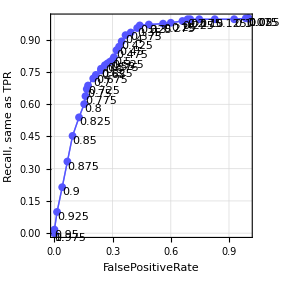
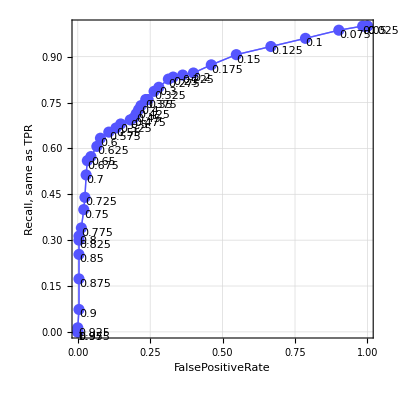
ROC plot(s): <|died→-Graphics-,survived→-Graphics-|>

In the specified pipeline computation the last column of the dataset is assumed to be the one with the class labels.

The ClCon functions are separated into four groups:

operations,

setters,

takers,

State Monad generic functions.

An overview of the those functions is given in the tables in next two sub-sections. The next section, “Monad elements”, gives details and examples for the usage of the ClCon operations.

## Monad elements

In this section we show that ClCon has all of the properties listed in the previous section.

### The monad head

The monad head is ClCon. Anything wrapped in ClCon can serve as monad’s pipeline value. It is better though to use the constructor ClConUnit. (Which adheres to the definition in [Wk1].)

```mathematica
ClCon[{{1,"a"},{2,"b"}},<||>]⟹ClConSummarizeData;
```

summaries:  {Anonymous→{1 column 1
1st Qu | 1
Min | 1
Mean | 1.5
Median | 1.5
3rd Qu | 2
Max | 2,2 column 2
a | 1
b | 1}}

### Lifting data to the monad

The function lifting the data into the monad ClCon is ClConUnit.

The lifting to the monad marks the beginning of the monadic pipeline. It can be done with data or without data. Examples follow.

```mathematica
ClConUnit[dsData]⟹ClConSummarizeData;
```

summaries:  {Anonymous→{1 number
Min | 20
1st Qu | 278
Mean | 531.17
Median | 531.5
3rd Qu | 801.5
Max | 998,2 feature1
1st Qu | 0
Min | 0
Mean | 0.92
Median | 1
3rd Qu | 2
Max | 2,3 feature2
Min | 0
1st Qu | 2
Mean | 4.27
Median | 4.5
3rd Qu | 6
Max | 9,4 label
0 | 40
2 | 32
1 | 28}}

```mathematica
ClConUnit[]⟹ClConSetTrainingData[dsData]⟹ClConSummarizeData;
```

summaries:  {trainingData→{1 number
Min | 20
1st Qu | 278
Mean | 531.17
Median | 531.5
3rd Qu | 801.5
Max | 998,2 feature1
1st Qu | 0
Min | 0
Mean | 0.92
Median | 1
3rd Qu | 2
Max | 2,3 feature2
Min | 0
1st Qu | 2
Mean | 4.27
Median | 4.5
3rd Qu | 6
Max | 9,4 label
0 | 40
2 | 32
1 | 28}}

(See the sub-section “Setters and takers” for more details of setting and taking values in ClCon contexts.)

Currently the monad can deal with data in the following forms:

datasets,

matrices,

lists of example→label rules.

The ClCon monad also has the non-monadic function ClConToNormalClassifierData which can be used to convert datasets and matrices to lists of example→label rules. Here is an example:

```mathematica
Short[ClConToNormalClassifierData[dsData],3]
```

{{639,0,9}→0,{121,1,1}→1,{309,0,9}→0,{648,0,8}→0,{995,2,5}→2,{127,1,7}→1,{908,2,8}→2,{564,0,4}→0,{380,2,0}→2,«82»,{449,2,9}→2,{522,0,2}→0,{288,0,8}→0,{51,0,1}→0,{108,0,8}→0,{76,1,6}→1,{706,1,6}→1,{765,0,5}→0,{195,0,5}→0}

When the data lifted to the monad is a dataset or a matrix it is assumed that the last column has the class labels. WL makes it easy to rearrange columns in such a way the any column of dataset or a matrix to be the last.

### Data splitting

The splitting is made with ClConSplitData, which takes up to two arguments and options. The first argument specifies the fraction of training data. The second argument -- if given -- specifies the fraction of the validation part of the training data. If the value of option Method is ”LabelsProportional”, then the splitting is done in correspondence of the class labels tallies. (”LabelsProportional” is the default value.) Data splitting demonstration examples follow.

Here are the dimensions of the dataset dsData:

```mathematica
Dimensions[dsData]
```

{100,4}

Here we split the data into 70% for training and 30% for testing and then we verify that the corresponding number of rows add to the number of rows of dsData:

```mathematica
val=ClConUnit[dsData]⟹ClConSplitData[0.7]⟹ClConTakeValue;
Map[Dimensions,val]
Total[First/@%]
```

<|trainingData→{69,4},testData→{31,4}|>

100

Note that if Method is not “LabelsProportional” we get slightly different results.

```mathematica
val=ClConUnit[dsData]⟹ClConSplitData[0.7,Method->"Random"]⟹ClConTakeValue;
Map[Dimensions,val]
Total[First/@%]
```

<|trainingData→{70,4},testData→{30,4}|>

100

In the following code we split the data into 70% for training and 30% for testing, then the training data is further split into 90% for training and 10% for classifier training validation; then we verify that the number of rows add up.

```mathematica
val=ClConUnit[dsData]⟹ClConSplitData[0.7,0.1]⟹ClConTakeValue;
Map[Dimensions,val]
Total[First/@%]
```

<|trainingData→{61,4},testData→{31,4},validationData→{8,4}|>

100

### Classifier training

The monad ClCon supports both single classifiers obtained with Classify and classifier ensembles obtained with Classify and managed with the package “ClassifierEnsembles.m”, [AAp4].

#### Single classifier training

With the following pipeline we take the Titanic data, split it into 75/25 % parts, train a Logistic Regression classifier, and finally take that classifier from the monad.

```mathematica
cf=
ClConUnit[dsTitanic]⟹
ClConSplitData[0.75]⟹
ClConMakeClassifier["LogisticRegression"]⟹
ClConTakeClassifier;
```

Here is information about the obtained classifier:

```mathematica
Information[cf,"TrainingTime"]
```

1.45126 s

If we want to pass parameters to the classifier training we can use the Method option. Here we train a Random Forest classifier with 400 trees:

```mathematica
cf=
ClConUnit[dsTitanic]⟹
ClConSplitData[0.75]⟹
ClConMakeClassifier[Method->{"RandomForest","TreeNumber"->400}]⟹
ClConTakeClassifier;
```

```mathematica
Information[cf,"TreeNumber"]
```

400

#### Classifier ensemble training

With the following pipeline we take the Titanic data, split it into 75/25 % parts, train a classifier ensemble of three Logistic Regression classifiers and two Nearest Neighbors classifiers using random sampling of 90% of the training data, and finally take that classifier ensemble from the monad.

```mathematica
ensemble=
ClConUnit[dsTitanic]⟹
ClConSplitData[0.75]⟹
ClConMakeClassifier[{{"LogisticRegression",0.9,3},{"NearestNeighbors",0.9,2}}]⟹
ClConTakeClassifier;
```

The classifier ensemble is simply an association with keys that are automatically assigned names and corresponding values that are classifiers.

```mathematica
ensemble
```

<|LogisticRegression[1,0.9]→ClassifierFunction[…],LogisticRegression[2,0.9]→ClassifierFunction[…],LogisticRegression[3,0.9]→ClassifierFunction[…],NearestNeighbors[1,0.9]→ClassifierFunction[…],NearestNeighbors[2,0.9]→ClassifierFunction[…]|>

Here are the training times of the classifiers in the obtained ensemble:

```mathematica
ClassifierInformation[#,"TrainingTime"]&/@ensemble
```

ClassifierInformation::mlobs: ClassifierInformation is obsolete. It has been superseeded by Information since version 12.

<|LogisticRegression[1,0.9]→1.21331 s,LogisticRegression[2,0.9]→1.42508 s,LogisticRegression[3,0.9]→1.22511 s,NearestNeighbors[1,0.9]→0.08632 s,NearestNeighbors[2,0.9]→0.084772 s|>

A more precise specification can be given using associations. The specification

```mathematica
<|"method"->"LogisticRegression","sampleFraction"->0.9,"numberOfClassifiers"->3,"samplingFunction"->RandomChoice|>
```

says “make three Logistic Regression classifiers, for each taking 90% of the training data using the function RandomChoice.”

Here is a pipeline specification equivalent to the pipeline specification above:

```mathematica
ensemble2=
ClConUnit[dsTitanic]⟹
ClConSplitData[0.75]⟹
ClConMakeClassifier[{<|"method"->"LogisticRegression","sampleFraction"->0.9,"numberOfClassifiers"->3,"samplingFunction"->RandomSample|>,<|"method"->"NearestNeighbors","sampleFraction"->0.9,"numberOfClassifiers"->2,"samplingFunction"->RandomSample|>}]⟹
ClConTakeClassifier;
```

```mathematica
ensemble2
```

<|LogisticRegression[1,0.9]→ClassifierFunction[…],LogisticRegression[2,0.9]→ClassifierFunction[…],LogisticRegression[3,0.9]→ClassifierFunction[…],NearestNeighbors[1,0.9]→ClassifierFunction[…],NearestNeighbors[2,0.9]→ClassifierFunction[…]|>

### Classifier testing

Classifier testing is done with the testing data in the context.

Here is a pipeline that takes the Titanic data, splits it, and trains a classifier:

```mathematica
p=
ClConUnit[dsTitanic]⟹
ClConSplitData[0.75]⟹
ClConMakeClassifier["DecisionTree"];
```

Here is how we compute selected classifier measures:

```mathematica
p⟹
ClConClassifierMeasurements[{"Accuracy","Precision","Recall","FalsePositiveRate"}]⟹
ClConTakeValue
```

<|Accuracy→0.7393,FalsePositiveRate→<|died→0.35,survived→0.203822|>,Precision→<|died→0.78125,survived→0.670103|>,Recall→<|died→0.796178,survived→0.65|>|>

(The measures are listed in the function page of ClassifierMeasurements.)

Here we show the confusion matrix plot:

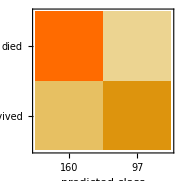
value:  <|ConfusionMatrixPlot→-Graphics-|>

```mathematica
p⟹ClConClassifierMeasurements["ConfusionMatrixPlot"]⟹ClConEchoValue;
```

Here is how we plot ROC curves by specifying the ROC parameter range and the image size:

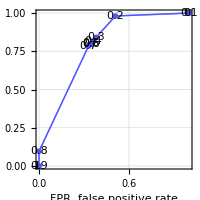
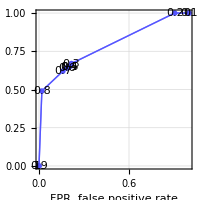
ROC plot(s):  <|died→-Graphics-,survived→-Graphics-|>

```mathematica
p⟹
ClConROCPlot["FPR","TPR","ROCRange"->Range[0,1,0.1],ImageSize->200];
```

Remark: ClCon uses the package ROCFunctions.m, [AAp5], which implements all functions defined in [Wk2].

Here we plot ROC functions values (y-axis) over the ROC parameter (x-axis):

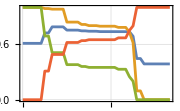
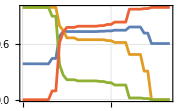
ROC line plot(s):  <|died→-Graphics-,survived→-Graphics-|>

```mathematica
p⟹ClConROCListLinePlot[{"ACC","TPR","FPR","SPC"}];
```

Note of the “ClConROC*Plot” functions automatically echo the plots. The plots are also made to be the pipeline value. Using the option specification “Echo”→False the automatic echoing of plots can be suppressed. With the option “ClassLabels” we can focus on specific class labels.

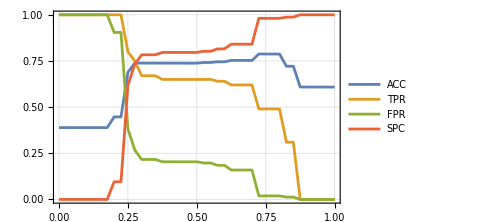
value:  <|survived→-Graphics-|>

```mathematica
p⟹
ClConROCListLinePlot[{"ACC","TPR","FPR","SPC"},"Echo"->False,"ClassLabels"->"survived",ImageSize->Medium]⟹
ClConEchoValue;
```

### Variable importance finding

Using the pipeline constructed above let us find the most decisive variables using systematic random shuffling (as explained in [AA3]):

```mathematica
p⟹
ClConAccuracyByVariableShuffling⟹
ClConTakeValue
```

<|None→0.7393,passenger class→0.692607,passenger age→0.750973,passenger sex→0.579767|>

We deduce that “passengerSex” is the most decisive variable because its corresponding classification success rate is the smallest. (See [AA3] for more details.)

Using the option “ClassLabels” we can focus on specific class labels:

```mathematica
p⟹
ClConAccuracyByVariableShuffling["ClassLabels"->"survived"]⟹
ClConTakeValue
```

<|None→{0.670103},passenger class→{0.575758},passenger age→{0.673267},passenger sex→{0.494505}|>

### Setters and takers

The values from the monad context can be set or obtained with the corresponding “setter” and “taker” functions as summarized in a previous section.

For example:

```mathematica
p⟹ClConTakeClassifier
```

ClassifierFunction[…]

```mathematica
Short[Normal[p⟹ClConTakeTrainingData]]
```

{<|passenger class→1st,passenger age→21.,passenger sex→female,passenger survival→survived|>,«979»,<|«1»|>}

```mathematica
Short[Normal[p⟹ClConTakeTestData]]
```

{<|passenger class→1st,passenger age→49.,passenger sex→female,passenger survival→survived|>,«326»,<|«1»|>}

```mathematica
p⟹ClConTakeVariableNames
```

{passenger class,passenger age,passenger sex,passenger survival}

If other values are put in the context they can be obtained through the (generic) function ClConTakeContext, [AAp1]:

```mathematica
p=ClConUnit[RandomReal[1,{2,2}]]⟹ClConAddToContext["data"];
```

```mathematica
(p⟹ClConTakeContext)["data"]
```

{{0.242911,0.960949},{0.8538,0.0117612}}

Another generic function from [AAp1] is ClConTakeValue (used many times above.)

## Example use cases

### Classification with MNIST data

Here we show an example of using ClCon with the reasonably large dataset of images MNIST, [YL1].

```mathematica
mnistData=ExampleData[{"MachineLearning","MNIST"},"Data"];
```

RandomGeneratorState[…]

summaries:  {trainingData→{1 column 1
-Graphics- | 1
-Graphics- | 1
-Graphics- | 1
-Graphics- | 1
-Graphics- | 1
-Graphics- | 1
(Other) | 13990}→{1 column 1
Min | 0
1st Qu | 2
Median | 4
Mean | 4.42948
3rd Qu | 7
Max | 9},testData→{1 column 1
-Graphics- | 1
-Graphics- | 1
-Graphics- | 1
-Graphics- | 1
-Graphics- | 1
-Graphics- | 1
(Other) | 5998}→{1 column 1
Min | 0
1st Qu | 2
Median | 4
Mean | 4.42921
3rd Qu | 7
Max | 9}}

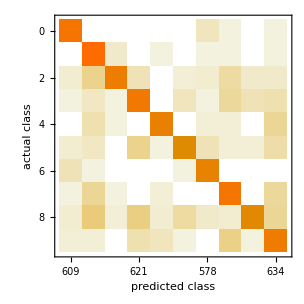
value:  <|Accuracy→0.948368,ConfusionMatrixPlot→-Graphics-|>

```mathematica
SeedRandom[3423]
p=
ClConUnit[RandomSample[mnistData,20000]]⟹
ClConSplitData[0.7]⟹
ClConSummarizeData⟹
ClConMakeClassifier["NearestNeighbors"]⟹
ClConClassifierMeasurements[{"Accuracy","ConfusionMatrixPlot"}]⟹
ClConEchoValue;
```

Here we plot the ROC curve for a specified digit:

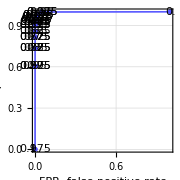
ROC plot(s):  <|5→-Graphics-|>

```mathematica
p⟹ClConROCPlot["ClassLabels"->5];
```

### Conditional continuation

In this sub-section we show how the computations in a ClCon pipeline can be stopped or continued based on a certain condition.

The pipeline below makes a simple classifier (“LogisticRegression”) for the WineQuality data, and if the recall for the important label (“high”) is not large enough makes a more complicated classifier (“RandomForest”). The pipeline marks intermediate steps by echoing outcomes and messages.

summaries:  {trainingData→{1 RowID
1 | 12
10 | 12
100 | 12
1000 | 12
1001 | 12
1002 | 12
(Other) | 35174,2 Variable
alcohol | 2938
chlorides | 2938
density | 2938
fixed acidity | 2938
free sulfur dioxide | 2938
pH | 2938
(Other) | 17618,3 Value
low | 2302
high | 636
0.28 | 340
0.3 | 314
0.32 | 305
0.26 | 284
(Other) | 31065},testData→{1 RowID
1 | 12
10 | 12
100 | 12
1000 | 12
1001 | 12
1002 | 12
(Other) | 14621,2 Variable
alcohol | 1225
chlorides | 1225
density | 1225
fixed acidity | 1225
free sulfur dioxide | 1225
pH | 1225
(Other) | 7343,3 Value
low | 960
high | 265
0.3 | 140
0.28 | 133
0.27 | 117
0.32 | 117
(Other) | 12961},validationData→{1 RowID
1 | 12
10 | 12
100 | 12
101 | 12
102 | 12
103 | 12
(Other) | 8746,2 Variable
alcohol | 735
chlorides | 735
density | 735
fixed acidity | 735
free sulfur dioxide | 735
pH | 735
(Other) | 4408,3 Value
low | 576
high | 159
0.28 | 85
0.3 | 82
0.34 | 75
0.32 | 71
(Other) | 7770}}

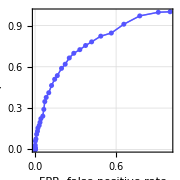
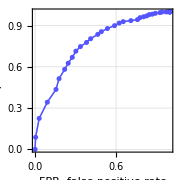
ROC plot(s):  <|high→-Graphics-,low→-Graphics-|>

value:  <|Accuracy→0.79102,FalsePositiveRate→<|high→0.0572917,low→0.758491|>,Precision→<|high→0.537815,low→0.818264|>,Recall→<|high→0.241509,low→0.942708|>|>

Info:  Recall for "high" not good enough... making a large random forest.

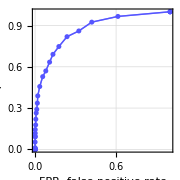
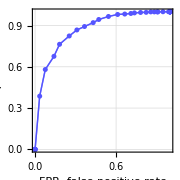
ROC plot(s):  <|high→-Graphics-,low→-Graphics-|>

value:  <|Accuracy→0.813878,FalsePositiveRate→<|high→0.00104167,low→0.856604|>,Precision→<|high→0.974359,low→0.8086|>,Recall→<|high→0.143396,low→0.998958|>|>

```mathematica
SeedRandom[267];
res=
ClConUnit[dsWineQuality[All, Join[#,<|"wineQuality"->If[#wineQuality≥7,"high","low"]|>]&]]⟹
ClConSplitData[0.75,0.2]⟹
ClConSummarizeData(* summarize the data *)⟹
ClConMakeClassifier[Method->"LogisticRegression"](* training a simple classifier *)⟹
ClConROCPlot["FPR","TPR","ROCPointCallouts"->False]⟹
ClConClassifierMeasurements[{"Accuracy","Precision","Recall","FalsePositiveRate"}]⟹
ClConEchoValue⟹
ClConIfElse[#["Recall","high"]>0.70& (* criteria based on the recall for "high" *),
ClConEcho["Good recall for \"high\"!","Success:"],
ClConUnit[##]⟹
ClConEcho[Style["Recall for \"high\" not good enough... making a large random forest.",Darker[Red]],"Info:"]⟹
ClConMakeClassifier[Method->{"RandomForest","TreeNumber"->400}](* training a complicated classifier *)⟹
ClConROCPlot["FPR","TPR","ROCPointCallouts"->False]⟹
ClConClassifierMeasurements[{"Accuracy","Precision","Recall","FalsePositiveRate"}]⟹
ClConEchoValue&];
```

We can see that the recall with the more complicated is classifier is higher. Also the ROC plots of the second classifier are visibly closer to the ideal one. Still, the recall is not good enough, we have to find a threshold that is better that the default one. (See the next sub-section.)

### Classification with custom thresholds

(In this sub-section we use the monad from the previous sub-section.)

Here we compute classification measures using the threshold 0.3 for the important class label (“high”):

```mathematica
res⟹
ClConClassifierMeasurementsByThreshold[{"Accuracy","Precision","Recall","FalsePositiveRate"},"high"->0.3]⟹
ClConTakeValue
```

<|Accuracy→0.853878,Precision→<|high→0.721649,low→0.878758|>,Recall→<|high→0.528302,low→0.94375|>,FalsePositiveRate→<|high→0.05625,low→0.471698|>|>

We can see that the recall for “high” is fairly large and the rest of the measures have satisfactory values. (The accuracy did not drop that much, and the false positive rate is not that large.)

Here we compute suggestions for the best thresholds:

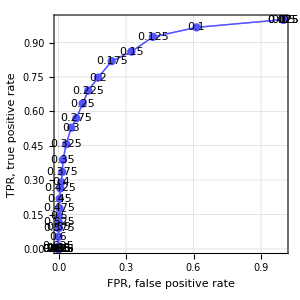
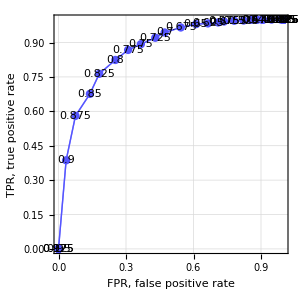
ROC plot(s):  <|high→-Graphics-,low→-Graphics-|>

value:  <|high→{0.175,0.2,0.225},low→{0.825,0.8,0.775}|>

```mathematica
res(* start with a previous monad *)⟹
ClConROCPlot[ImageSize->300](* make ROC plots *)⟹
ClConSuggestROCThresholds[3](* find the best 3 thresholds per class label *)⟹
ClConEchoValue(* echo the result *);
```

The suggestions are the ROC points that closest to the point {0,1} (which corresponds to the ideal classifier.)

Here is a way to use threshold suggestions within the monad pipeline:

```mathematica
res⟹
ClConSuggestROCThresholds⟹
ClConEchoValue⟹
(ClConUnit[##]⟹ClConClassifierMeasurementsByThreshold[{"Accuracy","Precision","Recall"},"high"->First[#1["high"]]]&)⟹
ClConEchoValue;
```

value:  <|high→{0.175},low→{0.825}|>

value:  <|Accuracy→0.77551,Precision→<|high→0.488739,low→0.93854|>,Recall→<|high→0.818868,low→0.763542|>|>

Related Guides

Classification pipeline functions

Related Tech Notes

Classification of MNIST data

## Metadata

### Categorization

Tech Note

AntonAntonov/MonadicContextualClassification

AntonAntonov`MonadicContextualClassification`

AntonAntonov/MonadicContextualClassification/tutorial/Classificationworkflowsmonad

### Keywords

Monad

Pipeline

Classification

Workflow